```mathematica
ClearAll["Global`*"]
```

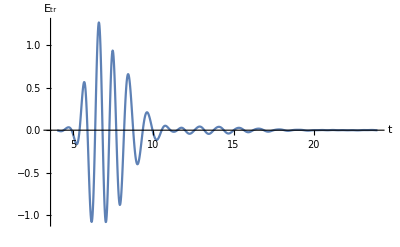

```mathematica
messyData=Import["C:\\Users\\79511\\OneDrive\\Документы\\GitHub\\Labs_Zalipaev\\lab_5\\epsdata.txt"];
lessMessyData=ToExpression@StringReplace[StringSplit[messyData],"e"->"*10^"];
data=Table[{lessMessyData[[i]],lessMessyData[[i+1]]},{i,1,Length[lessMessyData]-1,2}];
tmin=data[[1,1]];
tmax=data[[-1,1]];
ListLinePlot[data,PlotRange->All,AxesLabel->{"t","E_tr"}]
```

```mathematica
(*f[t_]:=Exp[-t^2/(4 Subscript[τ, p]^2)-I Subscript[ω, 0] t]
F[ω_]:=Integrate[Exp[I ω t] f[t],{t,-Infinity,Infinity}][[1]]*
```

```mathematica
z=10^-3;(*detector position*)
c=3*10^8;
factor=N@2 Pi z/c*10^11;
k0=1;
d=1;
interpOrder=3;
```

```mathematica
F[f_,τ_,f0_]:=2Sqrt[Pi] τ Exp[-2Pi (f-f0)^2 τ^2]
timeDomain=Transpose[data][[1]];
discreteExponent[f_]:=Transpose[{timeDomain,Exp[I (f t-factor)]/.{t->timeDomain}}]
multipliedFuncValues[f_]:=Transpose[data][[2]]*Transpose[discreteExponent[f]][[2]]
RealMultipliedFunction[f_]:=Transpose[{timeDomain,Re@multipliedFuncValues[f]}]
ImMultipliedFunction[f_]:=Transpose[{timeDomain,Im@multipliedFuncValues[f]}]
RealIntegral[f_]:=Integrate[Interpolation[RealMultipliedFunction[f],InterpolationOrder->interpOrder][t],{t,tmin,tmax}]
ImIntegral[f_]:=Integrate[Interpolation[ImMultipliedFunction[f],InterpolationOrder->interpOrder][t],{t,tmin,tmax}]
RealT[f_,τ_,f0_]:=(F[f,τ,f0])^-1*RealIntegral[f]
ImT[f_,τ_,f0_]:=(F[f,τ,f0])^-1*ImIntegral[f]
Φ[n_]:=(4n)/((n+1)^2 Exp[-I k0 n d]-(n-1)^2 Exp[I k0 n d])-T[f]
```

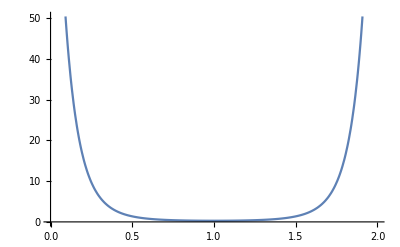

```mathematica
F[f_,τ_,f0_]:=2Sqrt[Pi] τ Exp[-2Pi (f-f0)^2 τ^2]
Plot[(F[f,1,1])^-1,{f,0,2}]
```

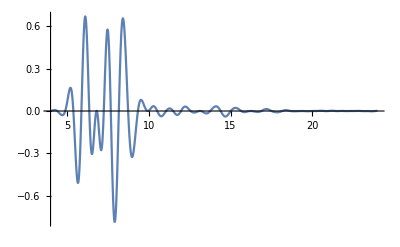

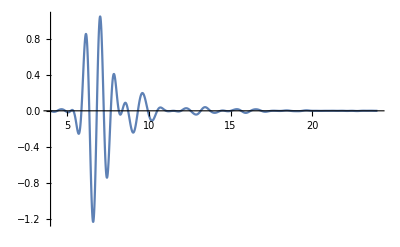

```mathematica
intfunc1=Interpolation[RealMultipliedFunction[1],InterpolationOrder->3];
intfunc2=Interpolation[ImMultipliedFunction[1],InterpolationOrder->3];
Plot[intfunc1[t],{t,tmin,tmax},PlotRange->All]
Plot[intfunc2[t],{t,tmin,tmax},PlotRange->All]
```

## Trying to fit model function (shit)

```mathematica
modelFunction=a Sin[b x]*Exp[-(x-c)^2/(2d^2)];
modelFit=Quiet@Transpose[NonlinearModelFit[data,modelFunction,{{a,1.5},{b,8},{c,7.5},{d,1}},x]["ParameterTable"][[1,1]]];
paramValuesArray=Transpose@Table[{modelFit[[1,i]],modelFit[[2,i]]},{i,2,5}];
rules=Table[paramValuesArray[[1,i]]->paramValuesArray[[2,i]],{i,1,Length[paramValuesArray[[1]]]}]
resultingFunction=modelFunction/.{rules}[[1]]
ListLinePlot[data,PlotRange->All]
Plot[resultingFunction,{x,4,24},PlotRange->All]
```